```mathematica
(***Note: Values for generating these plots are embedded within the raw data set, which is too large to upload onto the public data repository***)
```

```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
v2mColor=Purple;
```

```mathematica
(****V1 to V2m******)
```

```mathematica
dateMouseSessionList={{"091520","Mouse21060","Session1"},{"121420","Mouse23379","Session1"},{"101920","Mouse23392","Session1"},{"102620","Mouse23392","Session2"},{"020521","Mouse23320","Session2"},{"030121","Mouse23329","Session2"}};
```

```mathematica
(***Extract all the ROIs for this particular stimulus type***)
```

```mathematica
allROIsPerSession=Table[Range@Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/dFOverF0TimeSeries/"]]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
discardROIsList=Table[Flatten@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","discardROIs",".txt"],"List"]),{n,1,Length[dateMouseSessionList]}];
```

```mathematica
allROIsPerSession=Table[Complement[allROIsPerSession[[n]],discardROIsList[[n]]],{n,1,Length[allROIsPerSession]}];
```

```mathematica
sigRespGratingsROIsPerSession=Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","sigResponsiveROIs.txt"],"List"],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
sigRespGratingsROIsPerSession=Table[Complement[sigRespGratingsROIsPerSession[[n]],discardROIsList[[n]]],{n,1,Length[sigRespGratingsROIsPerSession]}];
```

```mathematica
nonSigROIsPerSession=Table[Complement[allROIsPerSession[[n]],sigRespGratingsROIsPerSession[[n]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
(***Extract all the visual responses for the ROIs extracted***)
```

```mathematica
visRespGratingsV1toV2m=Abs/@DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,sigRespGratingsROIsPerSession[[n]]}],{n,1,Length[sigRespGratingsROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespNonRespV1toV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,nonSigROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespAllV1toV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,allROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
(****LM to V2m******)
```

```mathematica
dateMouseSessionList={{"092321","Mouse22422","Session2"},{"100521","Mouse22422","Session2"},{"081721","Mouse22437","Session1"},{"081921","Mouse22437","Session2"},{"100421","Mouse22472","Session1"},{"102121","Mouse22422","Session1"},{"101721","Mouse22436","Session2"},{"071222","Mouse23025","Session1"},{"071122","Mouse23100","Session1"},{"070822","Mouse23014","Session2"},{"071522","Mouse23014","Session1"},{"070722","Mouse22518","Session2"},{"071322","Mouse22518","Session1"}};
```

```mathematica
(***Extract all the ROIs for this particular stimulus type***)
```

```mathematica
allROIsPerSession=Table[Range@Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/dFOverF0TimeSeries/"]]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
discardROIsList=Table[Flatten@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","discardROIs",".txt"],"List"]),{n,1,Length[dateMouseSessionList]}];
```

```mathematica
allROIsPerSession=Table[Complement[allROIsPerSession[[n]],discardROIsList[[n]]],{n,1,Length[allROIsPerSession]}];
```

```mathematica
sigRespGratingsROIsPerSession=Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","sigResponsiveROIs.txt"],"List"],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
sigRespGratingsROIsPerSession=Table[Complement[sigRespGratingsROIsPerSession[[n]],discardROIsList[[n]]],{n,1,Length[sigRespGratingsROIsPerSession]}];
```

```mathematica
nonSigROIsPerSession=Table[Complement[allROIsPerSession[[n]],sigRespGratingsROIsPerSession[[n]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
(***Extract all the visual responses for the ROIs extracted***)
```

```mathematica
visRespGratingsLMtoV2m=Abs/@DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,sigRespGratingsROIsPerSession[[n]]}],{n,1,Length[sigRespGratingsROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespNonRespLMtoV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,nonSigROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespAllLMtoV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,allROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
(****LP to V2m******)
```

```mathematica
dateMouseSessionList={{"120120","Mouse23377","Session2"},{"113020","Mouse23378","Session2"},{"120120","Mouse23378","Session2"},{"112920","Mouse23384","Session2"},{"113020","Mouse23384","Session2"},{"120120","Mouse23384","Session2"},{"102120","Mouse23394","Session2"},{"011921","Mouse23369","Session1"},{"011921","Mouse23339","Session1"},{"062922","Mouse23067","Session1"},{"062922","Mouse23075","Session2"},{"070822","Mouse23075","Session1"}};
```

```mathematica
(***Extract all the ROIs for this particular stimulus type***)
```

```mathematica
allROIsPerSession=Table[Range@Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/dFOverF0TimeSeries/"]]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
discardROIsList=Table[Flatten@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","discardROIs",".txt"],"List"]),{n,1,Length[dateMouseSessionList]}];
```

```mathematica
allROIsPerSession=Table[Complement[allROIsPerSession[[n]],discardROIsList[[n]]],{n,1,Length[allROIsPerSession]}];
```

```mathematica
sigRespGratingsROIsPerSession=Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","sigResponsiveROIs.txt"],"List"],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
sigRespGratingsROIsPerSession=Table[Complement[sigRespGratingsROIsPerSession[[n]],discardROIsList[[n]]],{n,1,Length[sigRespGratingsROIsPerSession]}];
```

```mathematica
nonSigROIsPerSession=Table[Complement[allROIsPerSession[[n]],sigRespGratingsROIsPerSession[[n]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
(***Extract all the visual responses for the ROIs extracted***)
```

```mathematica
visRespGratingsLPtoV2m=Abs/@DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,sigRespGratingsROIsPerSession[[n]]}],{n,1,Length[sigRespGratingsROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespNonRespLPtoV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,nonSigROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespAllLPtoV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,allROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
(****V2m******)
```

```mathematica
dateMouseSessionList={{"121619","Mouse20031","Session2"},{"121919","Mouse20033","Session1"},{"122219","Mouse20033","Session1"},{"092120","Mouse21011","Session1"},{"120720","Mouse23383","Session2"},{"022821","Mouse23310","Session1"},{"030321","Mouse23338","Session1"},{"031721","Mouse23338","Session1"}};
```

```mathematica
(***Extract all the ROIs for this particular stimulus type***)
```

```mathematica
allROIsPerSession=Table[Range@Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/dFOverF0TimeSeries/"]]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
sigRespGratingsROIsPerSession=Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","sigResponsiveROIs.txt"],"List"],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
nonSigROIsPerSession=Table[Complement[allROIsPerSession[[n]],sigRespGratingsROIsPerSession[[n]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
(***Extract all the visual responses for the ROIs extracted***)
```

```mathematica
visRespGratingsV2m=Abs/@DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,sigRespGratingsROIsPerSession[[n]]}],{n,1,Length[sigRespGratingsROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespNonRespV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,nonSigROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespAllV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,allROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
(**********************)
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[visRespAllV1toV2m,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{{-0.6,2},{-4,10}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[visRespAllV1toV2m,PlotRange->{{-0.5,0.9},{-4,10}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[-4,10,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[visRespAllLMtoV2m,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{{-0.6,2},{-4,10}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[visRespAllLMtoV2m,PlotRange->{{-0.5,0.9},{-4,10}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[-4,10,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[visRespAllLPtoV2m,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{{-0.6,2},{-4,10}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[visRespAllLPtoV2m,PlotRange->{{-0.5,0.9},{-4,10}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[-4,10,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
v2mAxonCharts=Show[BoxWhiskerChart[visRespAllV2m,{{"Whiskers", Directive[Darker@v2mColor,Thick]}, {"Fences", Directive[Darker@v2mColor,Thick]},{"MedianMarker", Directive[Darker@v2mColor,Thickness[0.009]]}},PlotRange->{{-0.6,2},{-4,10}},ChartStyle->Directive[v2mColor,Opacity[0.3]],Frame->False],DistributionChart[visRespAllV2m,PlotRange->{{-0.5,0.9},{-4,10}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v2mColor],Frame->False],FrameTicks->{{LinTicks[-4,10,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[visRespAllV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{{-0.64,2.0},{-4,10}},ChartStyle->Transparent,Frame->False],DistributionChart[visRespAllV2m,PlotRange->{{-0.5,0.9},{-4,10}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[-4,10,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

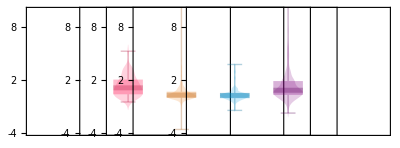

```mathematica
g=GraphicsRow[{v1AxonCharts,lmAxonCharts,lpAxonCharts,v2mAxonCharts,transp},Spacings->{{-280,-280,-280,-280,-480}},ImageSize->400]
```

```mathematica
PieChart[{Length[visRespNonRespV1toV2m],Length[visRespAllV1toV2m]-Length[visRespNonRespV1toV2m]},ChartBaseStyle->EdgeForm[{Thick,Black}],ChartStyle->{Lighter[v1Color,0.8],v1Color}]
```

-Graphics-

```mathematica
PieChart[{Length[visRespNonRespLMtoV2m],Length[visRespAllLMtoV2m]-Length[visRespNonRespLMtoV2m]},ChartBaseStyle->EdgeForm[{Thick,Black}],ChartStyle->{Lighter[lmColor,0.8],lmColor}]
```

-Graphics-

```mathematica
PieChart[{Length[visRespNonRespLPtoV2m],Length[visRespAllLPtoV2m]-Length[visRespNonRespLPtoV2m]},ChartBaseStyle->EdgeForm[{Thick,Black}],ChartStyle->{Lighter[lpColor,0.8],lpColor}]
```

-Graphics-

```mathematica
PieChart[{Length[visRespNonRespV2m],Length[visRespAllV2m]-Length[visRespNonRespV2m]},ChartBaseStyle->EdgeForm[{Thick,Black}],ChartStyle->{Lighter[v2mColor,0.8],v2mColor}]
```

-Graphics-